## Pre-calculus

## exponentials and logarithms

#### Not all exercises were implemented. I find it not interesting to work on items which I know that I can find a solution just by looking at them. I only do something if I do it for the first time or if it’s sufficiently different from previous exercises. This notebook is a prerequisite for learning Calculus and also a nice process for me to get my head around Mathematica.

## sketch the graph of f

### f(x) = 2^x

```mathematica
Plot[2^x, {x, -5, 5}]
```

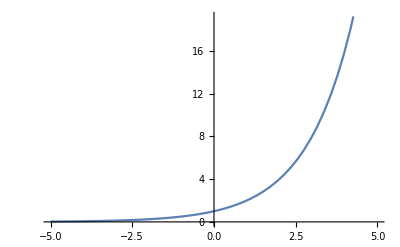

### f(x) = -3^x

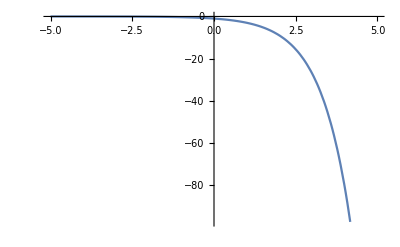

```mathematica
Plot[-3^x,{x, -5, 5}]
```

### f(x) = 2(5)^x

```mathematica
Plot[2(5)^x, {x, -5, 5}]
```

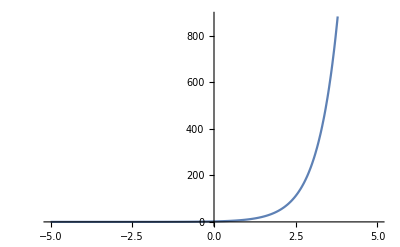

### f(x) = 7^x+ 3

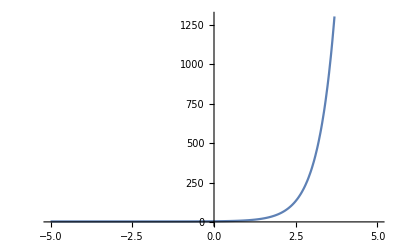

```mathematica
Plot[7^x+3, {x, -5, 5}]
```

### f(x) = 4^-x

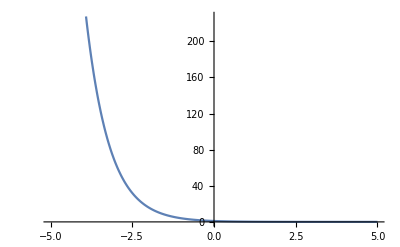

```mathematica
Plot[4^-x, {x, -5, 5}]
```

### f(x) = (1/2)^x

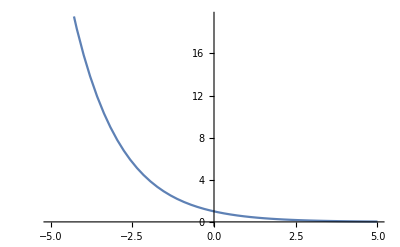

```mathematica
Plot[(1/2)^x, {x, -5, 5}]
```

## Solve the equations

### 5^(x + 8) = 5^(3x - 2)

5^(x + 8) = 5^(3x  -  2)
x + 8 = 3x - 2
x-3x = -2 -8
-2x = -10
2x = 10
x = 5

```mathematica
Solve[5^(x + 8) == 5^(3x - 2), x, Reals]
```

{{x→5}}

### 8^(7 - x)=8^(2x + 1)

8^(7 - x)=8^(2x + 1)
7 - x = 2x + 1
6 = 3x
x = 2

```mathematica
Solve[8^(7-x)==8^(2x+1), x, Reals]
```

{{x→2}}

### 5^(x^2)=5^(2x + 3)

5^(x^2)=5^(2x+3)
x^2=2x+3
x^2- 2x - 3 = 0
(x+1)(x-3) = 0
x_1= -1, x_2 = 3

```mathematica
Solve[5^(x^2)==5^(2x+3), x, Reals]
```

{{x→-1},{x→3}}

### 25^(x^2)= 5^(3x + 2)

5^(2 x^2)= 5^(3x + 2)
2 x^2 = 3x + 2
2 x^2 - 3x - 2 = 0

 I wasn’t  sure how to factor it, so just used Mathematica to factor
 
(x - 2) (2 x + 1) = 0

x_1= 2,  x_2= -(1/2)

```mathematica
Solve[25^(x^2)== 5^(3x + 2), x, Reals]
```

{{x→-1/2},{x→2}}

## Solve word problems

### A colony of an endangered species originally numbered 1,000 was predicted to have a population N after t years given by the equation N(t) = 1000(0.9)^t. Estimate population after: a) 1 year b) 5 years c) 10 years

```mathematica
1000(0.9)^1
1000(0.9)^5
1000(0.9)^10
```

900.

590.49

348.678

### The number of bacteria in a certain culture increased from 600 to 1800 between 8 am and 10 am. Assuming the growth is exponential, the number f(t) of bacteria t hours after 8 am is given by f(t) = 600(3)^(t/2). a) Estimate the number of bacteria at 9 am, 11 am, and noon. b) Sketch the graph of f

1039.23

3117.69

5400

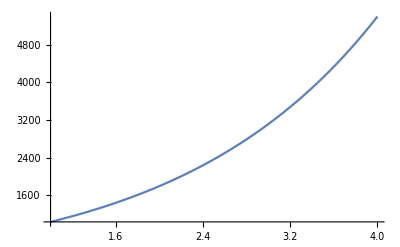

```mathematica
600 (3)^(1/2)// N
600(3)^(3/2)//N
600 (3)^2
Plot[600(3)^(t/2), {t, 1, 4}]
```

### An important problem in oceanography is to determine the amount of light that can penetrate to various ocean depths. The Beer - Lambert law asserts that the exponential function given by I(x) = I_0 c^x is a model for this phenomenon. For a certain location, I(x) = 10(0.4)^x is the amount of light (in calories/cm^2/sec) reaching a depth of x meters. a) Find the amount of light at a depth of 2 m. b) Sketch the graph of I for 0 ≤ x ≤ 5.

1.6

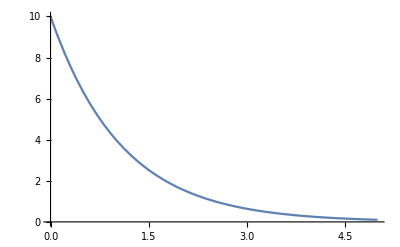

```mathematica
10(0.4)^2
Plot[10(0.4)^x, {x, 0, 5} ]
```

## Change to logarithmic form

### 5^3= 125

x = log_5 125

### 3^x= 7 + t

x = log_3(7+t)

### 5^-3= 1/125

x = log_5(1/125)

## Change to exponential form

### log_2 32 = 5

2^5 = 32

### log_7 m = 5x + 3

7^(5x + 3) = m

### log_2(1/64) = -6

2^-6= 1/64

## Solve for t using logarithms with base a

### 2 a^(t/5)= 5

t/5= log_(2a)5
t = 5 log_(2a)5 
Let’s check the solution for a = 4

```mathematica
t = 5Log[8, 5]// N;
8^(t/5)== 5
```

True

### 5 a^(3t)= 63

3t = log_(5a)(63)
t = (log_(5a(63)))/3

### A = Ba^Ct+ D

Ba^Ct = A - D
Ct = Log_Ba(A-D)
t = (Log_Ba(A - D))/C

## Find the numbers, if possible

### Log_9(-3)

Yes, it’s possible, LOL.

```mathematica
Log[9,-3]
```

(ⅈ π+Log[3])/Log[9]

## Solve the logarithmic equation

### log_4 x = log_4(8 - x)

x = 8 -x
2x = 8
x = 4

## Word problems II

#### The loudness of a sound, as experienced by the human ear, is based on its intensity level. The intensity level α (in decibels) that corresponds to a sound intensity I is α = 10log(I/I_0), where I_0 is a special value of I agreed to be the weakest sound that can be detected by the human ear under certain conditions. Find α if a) I is 10 times as great as I_0 b) I is 1000 times as great as I_0

a) α = 10log 10; α = 10;
b) α = 10 log1000; α = 30;

### A sound intensity level of 140 decibels produces pain in the average human ear. Approximately how many times greater than I_0 must I be in order for α to reach this level?

α = 10log(I/I_0)
140 = 10log(I/I_0)
log(I/I_0) = 14
(I/I_0) = 10^14

## Conic sections

## First of all, some conic section plots

### Circle section

```mathematica
gcone=Graphics3D[{Opacity[0.5], Cone[]}, Boxed-> False];
gplane=ContourPlot3D[0x + 0 y + 10z == 0,{x,-1,1},{y,-1,1}, {z, -1, 1}, ContourStyle->{Pink}];
Show[gcone, gplane]
```

-Graphics3D-

### Ellipse section

```mathematica
gcone=Graphics3D[{Opacity[0.5], Cone[]}, Boxed -> False];
gplane=ContourPlot3D[-1x + 2 y - 3z == 0,{x,-1,1},{y,-1,1}, {z, -1, 1}, ContourStyle->{Pink}];
Show[gcone, gplane]
```

-Graphics3D-

### Parabola section

```mathematica
gcone=Graphics3D[{Opacity[0.5], Cone[]}, Boxed->False];
gplane=ContourPlot3D[-1x + y - 0.8z == 0,{x,-1,1},{y,-1,1}, {z, -1, 1}, ContourStyle->{Pink}];
Show[gcone, gplane]
```

-Graphics3D-

### Hyperbola section

```mathematica
gcone=Graphics3D[{Opacity[0.5], Cone[]}, Boxed->False];
gplane=ContourPlot3D[x -0.16y - 0z == 0.5,{x,-1,1},{y,-1,1}, {z, -1, 1}, ContourStyle->{Pink, Opacity[0.7]}];
Show[gcone, gplane]
```

## Find the vertex, the focus and the directrix of the parabola. Sketch its graph, showing the focus and the directrix

### y = -1/12 x^2

This equation has the form y = ax^2 with a = -1/12. 
a = 1/(4p) so p = 1/(4a) ;  p = 1/(4(-1/12)) = 1/(-4/12)= 1/(-1/3)= -3; 
Vertex = (0, 0); Focus = (0, -3); Directrix is y = 3;

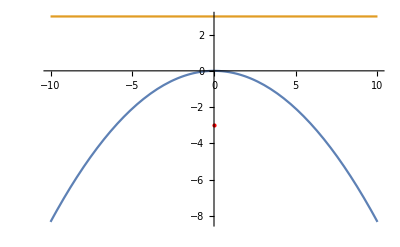

```mathematica
focus = Graphics[{PointSize[Large],Red,Point[{0, -3}]}];
parabola = Plot[{-1/12 x^2, y=3}, {x, -10, 10}];
Show[parabola, focus]
```

### 2 y^2= -3x

We can rewrite this as  -3x = 2 y^2
Divide both ends by -3 
x = -2/3 y^2
This equation has the form x=ay^2 with 	a= -2/3
a = 1/(4p),  so p = 1/(4a)
p = 1/(4(-2/3))= 1/(-8/3) = -3/8
Vertex = (0, 0); Focus = (-3/8, 0); Directrix is x=3/8

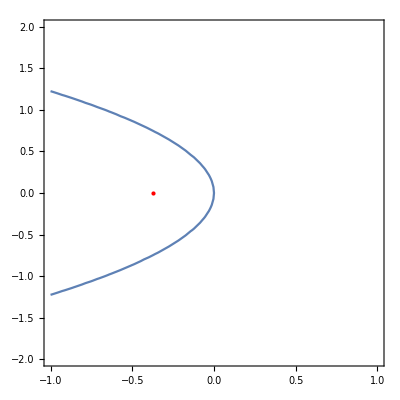

```mathematica
focus = Graphics[{PointSize[Large], Red, Point[{-3/8, 0}]}];
parabola = ContourPlot[{2 y^2 == -3x}, {x, -1, 1}, {y, -2, 2}, Axes-> True, GridLines -> {{{3/8, {Red, Dashed, Thick}}}, None}];

Show[parabola, focus]
```

### y^2= -100x

We can rewrite this as -100x = y^2
Divide both ends by -100
x = -1/100 y^2
This equation has the form x = ay^2 with a = -1/100
a = 1/(4p), so p = 1/(4a)
p = 1/(4(-1/100))= 1/(-4/100)= -100/4= -25
Vertex = (0, 0); Focus = (-25, 0); Directrix is x = 25

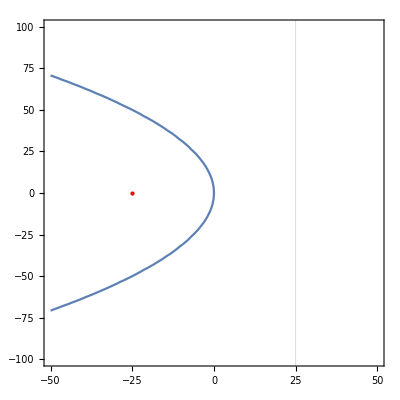

```mathematica
focus = Graphics[{PointSize[Large], Red, Point[{-25, 0}]}];
parabola = ContourPlot[{y^2 == -100x}, {x, -50, 50}, {y, -100, 100}, Axes-> True, GridLines -> {{{25, {Red, Dashed, Thick}}}, None}];

Show[parabola, focus]
```